# Enter title here

## Enter subtitle here

Enter subsubtitle here

Enter author here

Enter department here

Enter date here

## Enter section title here

### Enter subsection title here

In this notebook i will use the basic functionality of NDEigensystem to evaluate the eigenvalues and eigenfunctions of a Schrodinger operator
you see the Evalues increase in discreet chunks. This is another way to approach quantization.

{0.500041,1.50028,2.50096,3.50207,4.50206}

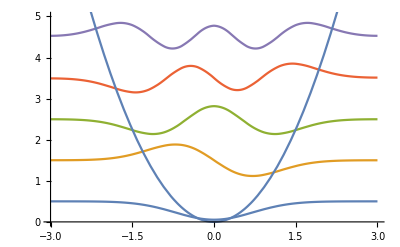

```mathematica
h=1/2;V[x_]:=x^2
l=-h^2*u''[x]+V[x]*u[x];
{Evalues,Efunctions}=NDEigensystem[l,u[x],{x,-3,3},5];
Evalues
Show[Plot[Evaluate[h*Efunctions+Evalues],{x,-3,3}],Plot[V[x],{x,-3,3}],PlotRange->{{-3,3},{0,5}},AxesOrigin->{-3,0}]
```

{0.0065389,-0.0185554,-0.0339309,0.0387839,-0.0480053}

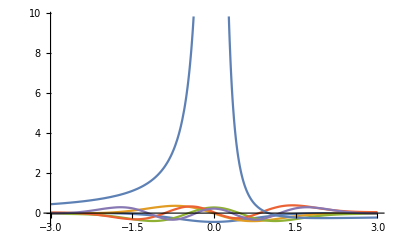

```mathematica
l = 1;h=1/2;V[x_]:=-1/x+l(l+1)/(2x^2)
L=-h^2*u''[x]+V[x]*u[x];
{Evalues,Efuncions}=NDEigensystem[L,u[x],{x,.01,30},5];
Evalues
Show[Plot[Evaluate[h*Efunctions+Evalues],{x,-3,3}],Plot[V[x],{x,-3,3}],AxesOrigin->{-3,0},PlotRange->All]
```